```mathematica
(*InverseFourierTransform[Cos[k],k,x]*)
```

√(π/2) DiracDelta[-1+x]+√(π/2) DiracDelta[1+x]

```mathematica
Func[x_]:=Cos[5x]+Cos[2x]
```

```mathematica
FT=FourierTransform[Func[x],x,k]
```

√(π/2) DiracDelta[-5+k]+√(π/2) DiracDelta[-2+k]+√(π/2) DiracDelta[2+k]+√(π/2) DiracDelta[5+k]

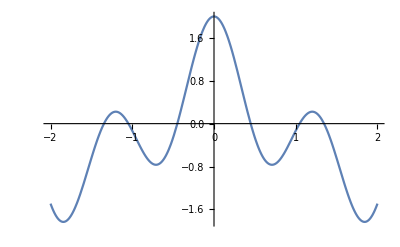

```mathematica
Plot[Func[x],{x,-2,2}]
```

```mathematica
InverseFourierTransform[FT E^(-k^2 R^2),k,x]
```

1/2 ⅇ^(-100-5 ⅈ x) (1+ⅇ^(84+3 ⅈ x)+ⅇ^(84+7 ⅈ x)+ⅇ^(10 ⅈ x))

```mathematica
R=2
```

2

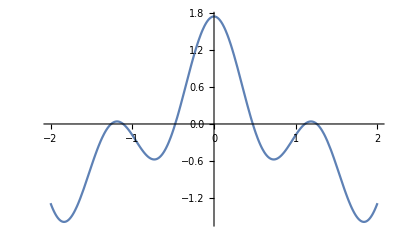

```mathematica
Plot[0.9607894391523232 Cos[2 x]+0.7788007830714049 Cos[5 x],{x,-2,2}]
```